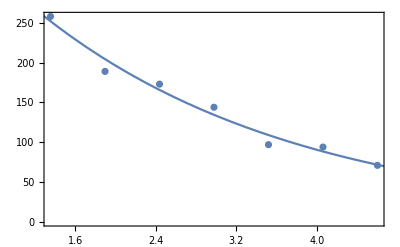

```mathematica
data=Import[NotebookDirectory[]<>"Mathematica_format.txt","Table"];
nlm =NonlinearModelFit[data,a ⅇ^(-t/τ),{a,τ},t];
Normal[nlm];
Show[ListPlot[data],Plot[nlm[x],{x,0,7}],Frame->True]
```